```mathematica
MainFunc[mF_,nF_,R1F_,bShow_]:=Module[{i,j,k,m,n},
m=mF;n=nF;R1=R1F;
H=VN/(π*R1^2);
Φ0[p_,r_]=BesselI[0,p*r];
Φ1[p_,r_]=D[Φ0[p,r],{r,1}];
Ψ0[q_,r_]=BesselI[0,q*r]/(q*BesselI[1,q*R1]+αDivλ*BesselI[0,q*R1])+BesselK[0,q*r]/(q*BesselK[1,q*R1]-αDivλ*BesselK[0,q*R1]);
Ψ1[q_,r_]=D[Ψ0[q,r],{r,1}];
δpMax=0;
δqMax=0;
p0Appr=√(αDivλ/H)*(1-1/6*H*αDivλ+11/360*H^2*αDivλ^2-17/5040*H^3*αDivλ^3-281/604800*H^4*αDivλ^4+44029/119750400*H^5*αDivλ^5);
Replp=FindRoot[p*Sin[p*H]-αDivλ*Cos[p*H]==0,{p,p0Appr}][[1]];
p0Exac=ReplaceAll[p,Replp];
δp=Abs[p0Appr/p0Exac-1];
If[δpMax<δp,δpMax=δp];
μ00=1/2*(H+αDivλ*Cos[p0Appr*H]^2/p0Appr^2);
mp={p0Appr};
mμ={μ00};
For[i=1,i≤m,i++,
iπ=i*π;
piAppr=iπ/H+αDivλ/iπ-(H αDivλ^2)/iπ^3-(H^2 (-6+iπ^2) αDivλ^3)/(3 iπ^5)+(H^3 (-15+4 iπ^2) αDivλ^4)/(3 iπ^7);
Replp=FindRoot[p*Sin[p*H]-αDivλ*Cos[p*H]==0,{p,piAppr}][[1]];
piExac=ReplaceAll[p,Replp];
δp=Abs[piAppr/piExac-1];
If[δpMax<δp,δpMax=δp];
AppendTo[mp,piAppr];
μii=1/2*(H+αDivλ*Cos[piAppr*H]^2/piAppr^2);
AppendTo[mμ,μii];
];
q0Appr=√((2*αDivλ)/H)*(1-1/12*H αDivλ+11/1440*H^2 αDivλ^2-17/40320*H^3 αDivλ^3-281/9676800*H^4 αDivλ^4+44029/3832012800*H^5 αDivλ^5);
Replq=FindRoot[(q-αDivλ^2/q)*Sin[q*H]-2*αDivλ*Cos[q*H]==0,{q,q0Appr}][[1]];
q0Exac=ReplaceAll[q,Replq];
δq=Abs[q0Appr/q0Exac-1];
If[δqMax<δq,δqMax=δq];
ν00=1/2*(H*(1+αDivλ^2/q0Appr^2)+αDivλ/q0Appr^2*(1+((q0Appr^2+αDivλ^2)/(q0Appr^2-αDivλ^2))^2*Cos[q0Appr*H]^2));
mν={ν00};
mq={q0Appr};
For[j=1,j≤n,j++,
jπ=j*π;
qjAppr=jπ/H+(2 αDivλ)/jπ-(4 H αDivλ^2)/jπ^3-(2 H^2 (-24+jπ^2) αDivλ^3)/(3 jπ^5)+(16 H^3 (-15+jπ^2) αDivλ^4)/(3 jπ^7);
Replq=FindRoot[(q-αDivλ^2/q)*Sin[q*H]-2*αDivλ*Cos[q*H]==0,{q,qjAppr}][[1]];
qjExac=ReplaceAll[q,Replq];
δq=Abs[qjAppr/qjExac-1];
If[δqMax<δq,δqMax=δq];
AppendTo[mq,qjAppr];
νjj=1/2*(H*(1+αDivλ^2/qjAppr^2)+αDivλ/qjAppr^2*(1+((qjAppr^2+αDivλ^2)/(qjAppr^2-αDivλ^2))^2*Cos[qjAppr*H]^2));
AppendTo[mν,νjj];
];
mκ=Table[0,{i,0,m},{j,0,n}];
For[i=0,i≤m,i++,
For[j=0,j≤n,j++,
κij=αDivλ/(mq[[j+1]]^2-mp[[i+1]]^2);
mκ[[i+1,j+1]]=κij;
];
];
mA=Table[0,{i,1,m+n+2},{j,1,m+n+3}];
mAI=Table[0,{i,1,m+n+2},{j,1,m+n+3}];
mAII=Table[0,{i,1,m+n+2},{j,1,m+n+3}];
For[k=1,k≤m+1,k++,
mA[[k,k]]=Φ0[mp[[k]],R0]/Φ1[mp[[k]],R0]*mμ[[k]];
mAI[[k,k]] = D[[mA[k,k]],{R1,1}];
mAII[[k,k]] = D[[mA[k,k]],{R1,2}];
For[j=0,j≤n,j++,
mA[[k,j+m+2]]=-Ψ0[mq[[j+1]],R0]/Ψ1[mq[[j+1]],R0]*mκ[[k,j+m+2]];
mAI[[k,j+m+2]] = D[[mA[k,j+m+2]],{R1,1}];
mAII[[k,j+m+2]] = D[[mA[k,j+m+2]],{R1,2}];
];
mA[[k, m + n + 3]]=-1/(λ*mp[[k]]^2);
mAI[[k, m + n + 3]] = D[[mA[k, m + n + 3]],{R1,1}];
mAII[[k, m + n + 3]] = D[[mA[k, m + n + 3]],{R1,2}];
];
For[k=m+2,k≤m+n+2,k++,
mA[[k,k]]=-mν[[k-m-1]];
mAI[[k,k]] = D[[mA[k,k]],{R1,1}];
mAII[[k,k]] = D[[mA[k,k]],{R1,2}];
For[i=0,i≤m,i++,
mA[[k,i+1]]=mκ[[i+1,k-m-1]];
mAI[[k,i + 1]] = D[[mA[k, i+ 1]],{R1,1}];
mAII[[k, i+ 1]] = D[[mA[k, i+ 1]],{R1,2}];
Print[mA[[k,i+1]]," ",mAI[[k,i+1]]," ",mAII[[k,i+1]]];
];
];
mX=MyLinearSolve[mA,mAI, mAII];
s=0;
For[i=0,i≤m,i++,
s+=mX[[i+1, 0]]/mp[[i+1]]^2;
s+=mX[[i+1, 1]]/mp[[i+1]]^2;
s+=mX[[i+1, 2]]/mp[[i+1]]^2;
];
ΘAvg=s*2/R0+1/α+H/λ;
RH0=ΘAvg/(π*R0^2);
If[bShow,
Print["R1=",R1,"  H=",H,"  RH=",RH0];
];
RH0
]
```

```mathematica
D[1/y1[x1],{x1,1}]
D[1/y1[x1],{x1,2}]
```

-y1'[x1]/y1[x1]^2

(2 y1'[x1]^2)/y1[x1]^3-y1''[x1]/y1[x1]^2

```mathematica
MyLinearSolve[A0_,A1_,A2_]:=Module[{i,j,m,n,r0,r1,r2,A0ii,A1ii,A2ii,A0ij,A1ij,A2ij},
m=Dimensions[A0][[1]];n=Dimensions[A0][[2]];
If[m≠n+1,
Print["Wrong Matrix!"];Return[];
];
For[i=1,i≤m,i++,
A0ii=A0[[i,i]];A1ii=A1[[i,i]];A2ii=A2[[i,i]];
r0=1/A0ii;r1=-r0^2*A1ii;r2=r0^2*(2*r0*A1ii^2-A2ii);
For[j=i+1,j≤n,j++,
A0ij=A0[[i,j]];A1ij=A1[[i,j]];A2ij=A2[[i,j]];
A0[[i,j]]=A0ij*r0;
A1[[i,j]]=A1ij*r0+A0ij*r1;
A2[[i,j]]=A2ij*r0+2*A1ij*r1+A0ij*r2;
];
A0[[i,i]]=1;A1[[i,i]]=0;A2[[i,i]]=0;

];
A0
]
```

```mathematica
MainCircle[mF_,nF_]:=Module[{},
α=10.0;
λ=236;
αDivλ=α/λ;
H=0.003;
R0=0.01;R1=0.05;
VN=π*R1^2*H;
VN=0.00002;
Print["VN=",VN];
bWas=False;
mG={};
dR1=0.001;
For[R1=0.048,R1≤0.162,R1+=dR1,
RH=MainFunc[mF,nF,R1,False];
If[bWas,
If[RHMin>RH,
R1Min=R1;RHMin=RH;
];
,
R1Min=R1;RHMin=RH;
bWas=True;
];
AppendTo[mG,{R1,RH}];
];
HMin=VN/(π*R1Min^2);
(*Print["R1Min=",R1Min,"  HMin=",HMin,"  RHMin=",RHMin];*)
ListPlot[mG,PlotJoined->True];
ak=R1Min-dR1;
RHak=MainFunc[mF,nF,ak,False];
bk=R1Min+dR1;
RHbk=MainFunc[mF,nF,bk,False];
ck=(3-Sqrt[5])*0.5*(bk-ak)+ak;
RHck=MainFunc[mF,nF,ck,False];
dk=(Sqrt[5]-1)*0.5*(bk-ak)+ak;
RHdk=MainFunc[mF,nF,dk,False];
Eps=0.00001;
i=10;
While[True,
If[RHck<=RHdk,
bk=dk;RHbk=RHdk;
dk=ck;RHdk=RHck;
ck=(3-Sqrt[5])*0.5*(bk-ak)+ak;
RHck=MainFunc[mF,nF,ck,False];
,
ak=ck;RHak=RHck;
ck=dk;RHck=RHdk;
dk=(Sqrt[5]-1)*0.5*(bk-ak)+ak;
RHdk=MainFunc[mF,nF,dk,False];
];
(*Print["ak=",ak,"  RHak=",RHak,"  bk=",bk,"  RHbk=",RHbk];*)
If[bk-ak<Eps,Break[]];
];
R1Min=(ak+bk)*0.5;
RHMin=MainFunc[mF,nF,R1Min,False];
HMin=VN/(π*R1Min^2);
(*Print["R1Min=",R1Min,"  HMin=",HMin,"  RHMin=",RHMin];*)
]
```

```mathematica
MainCircle[5,5]
mG0505=mG;
Put[mG0505,"./mG0505.txt"];
G0505=ListPlot[mG0505,PlotJoined->True,PlotStyle->{RGBColor[1,0,1],Thickness[0.003]},ImageSize->100];
```

VN=0.00002

```mathematica
δpMax
δqMax
```

1.11022×10^-16

2.22045×10^-16

```mathematica
MainCircle[10,10]
mG1010=mG;
Put[mG1010,"./mG1010.txt"];
G1010=ListPlot[mG1010,PlotJoined->True,PlotStyle->{RGBColor[1,1,0],Thickness[0.003]},ImageSize->100];
```

VN=0.00002

```mathematica
δpMax
δqMax
```

2.22045×10^-16

2.22045×10^-16

```mathematica
mG0505=Get["./mG0505.txt"];
mG1010=Get["./mG1010.txt"];
```

```mathematica
mG020805=Get["./mG020805.txt"];
mG041610=Get["./mG041610.txt"];
mG062415=Get["./mG062415.txt"];
mG1010=Get["./mG1010.txt"];
```

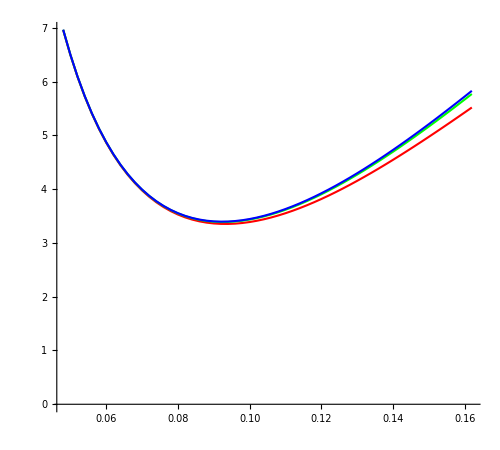

```mathematica
G020805=ListPlot[mG020805,PlotJoined->True,PlotStyle->{RGBColor[1,0,0],Thickness[0.003]},ImageSize->100];
G041610=ListPlot[mG041610,PlotJoined->True,PlotStyle->{RGBColor[0,1,0],Thickness[0.003]},ImageSize->100];
G062415=ListPlot[mG062415,PlotJoined->True,PlotStyle->{RGBColor[0,0,1],Thickness[0.003]},ImageSize->100];
G1010=ListPlot[mG1010,PlotJoined->True,PlotStyle->{RGBColor[0,0,0],Thickness[0.003]},ImageSize->100];
Show[G020805,G041610,G062415,G0505,ImageSize->500,AspectRatio->0.9]
```